```mathematica
ClearAll["Global``*"]
```

```mathematica
A={{341/125, 201/125, 68/25}, {-216/125, -201/125, -43/25}, {-216/125, -76/125, -43/25}}
B={{-1}, {1}, {1}}
C1={{-4, -2, -2}}
```

{{341/125,201/125,68/25},{-216/125,-201/125,-43/25},{-216/125,-76/125,-43/25}}

{{-1},{1},{1}}

{{-4,-2,-2}}

## 1.Calcolo dei modi naturali del sistema

```mathematica
λ= Eigenvalues[A]
```

{-1/5,-1/5,-1/5}

```mathematica
NullSpace[λ IdentityMatrix[3]-A]
```

{{-19/24,-1/4,1}}

Notiamo inoltre come la matrice A  non sia diagonalizzabile poiche   possiamo considerare fallito il test di diagonalizzabilità. Per procedere dobbiamo ricorre per la prima volta alla forma canonica di Jordan , con la funzione JordanDecomposition che ci restituisce due matrici, la prima è la matrice di cambiamento di base che ha per colonne gli autovettori legati ai blocchi di jordan e per seconda la matrice in forma canonica di jordan. Potremmo effettuare anche un altro test detto “del polinomio minimo”

```mathematica
Factor[CharacteristicPolynomial[A,x]]
```

-1/125 (1+5 x)^3

Avendo un solo autovalore vediamo che tutti e tre i modi generati sono associati a lui. Applicando Jordan ci aspettiamo di trovare una matrice 3x3 con un unico blocco poichè vi è un unico autovalore con m.a pari a 3.

```mathematica
{T,Λ}=JordanDecomposition[A]
```

{{{-19/24,-325/288,2375/3456},{-1/4,25/16,-125/64},{1,0,0}},{{-1/5,1,0},{0,-1/5,1},{0,0,-1/5}}}

```mathematica
Λ//MatrixForm
```

(-1/5 | 1 | 0
0 | -1/5 | 1
0 | 0 | -1/5)

```mathematica
MatrixPower[Λ,k]//MatrixForm
```

((-1/5)^k | -(-1)^k 5^(1-k) k | 1/2 (-1)^k 5^(2-k) (-1+k) k
0 | (-1/5)^k | -(-1)^k 5^(1-k) k
0 | 0 | (-1/5)^k)

Facendo la potenza della matrice mettiamo in evidenza i modi naturali del sistemahe sono come ipotizzato  tre cioè  (a meno di semplificazioni di Mathematica)

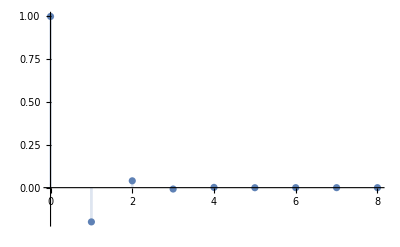

```mathematica
DiscretePlot[(-1/5)^k,{k,0,8},PlotRange->All]
```

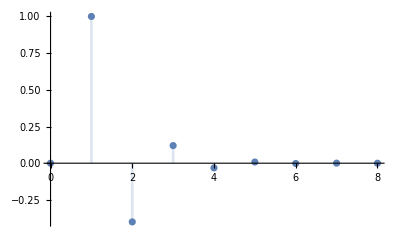

```mathematica
DiscretePlot[Binomial[k,1](-1/5)^(k-1),{k,0,8},PlotRange->All]
```

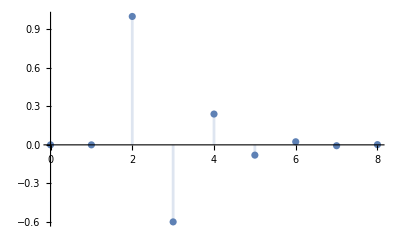

```mathematica
DiscretePlot[Binomial[k,2](-1/5)^(k-2),{k,0,8},PlotRange->All]
```

## 2.Calcolo della risposta libera

```mathematica
Subscript[x, 0]= {{-2},{-3},{0}}
```

{{-2},{-3},{0}}

```mathematica
T//MatrixForm
```

(-19/24 | -325/288 | 2375/3456
-1/4 | 25/16 | -125/64
1 | 0 | 0)

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{0},{132/25},{144/25}}

Calcolo la risposta libera nello stato :

```mathematica
Subscript[x, l][k_]:=Simplify[T.MatrixPower[Λ,k].Subscript[z, 0]]
```

```mathematica
Subscript[x, l][k]
```

{{(-1/5)^(1+k) (10-552 k+285 k^2)},{-3 (-1)^k 5^(-1-k) (5+34 k+30 k^2)},{12 (-1)^k 5^(-1-k) k (-41+30 k)}}

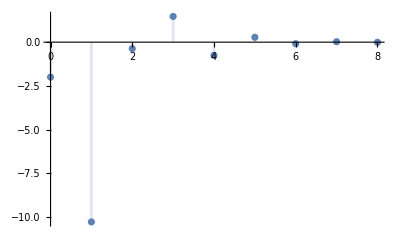

```mathematica
DiscretePlot[{Subscript[x, l][k][[1]]},{k,0,8},PlotRange->All]
```

Calcolo la risposta libera nell’uscita :

```mathematica
Subscript[y, l][k_]:=Simplify[C1.Subscript[x, l][k]]
```

```mathematica
Subscript[y, l][k]
```

{{2 (-1/5)^k (7-102 k+60 k^2)}}

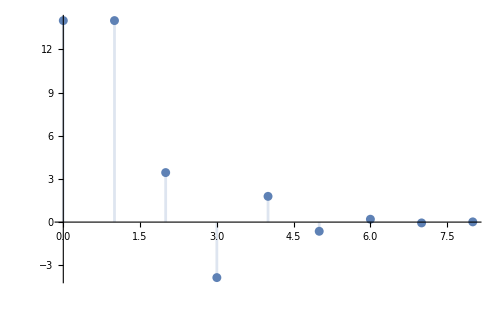

```mathematica
DiscretePlot[{Subscript[y, l][k][[1]]},{k,0,8},PlotRange->All]
```

## 3. Studiare la configurazione degli stati iniziali che attivano sulla risposta libera alcuni modi naturali ed altri no

Teniamo presente che abbiamo un solo autovalore che genera i modi naturali.Riportiamo T

```mathematica
T//MatrixForm
```

(-19/24 | -325/288 | 2375/3456
-1/4 | 25/16 | -125/64
1 | 0 | 0)

caso 1. Troviamo delle condizioni iniziali linearmente dipendente dalla prima colonna e che dunque annulla le due restanti

```mathematica
Subscript[x, 1]= 2{{T[[1,1]]},{T[[2,1]]},{T[[3,1]]}}
```

{{-19/12},{-1/2},{2}}

```mathematica
Subscript[z, 1]=Inverse[T].Subscript[x, 1]
```

{{2},{0},{0}}

```mathematica
Subscript[x, l1][k_]:=Simplify[T.MatrixPower[Λ,k].Subscript[z, 1]]
```

```mathematica
Subscript[x, l1][k]
```

{{-19/12 (-1/5)^k},{-1/2 (-1/5)^k},{2 (-1/5)^k}}

```mathematica
Subscript[y, l1][k_]:= Simplify[C1.Subscript[x, l1][k]];Subscript[y, l1][k]
```

{{2/3 (-1)^k 5^(1-k)}}

caso 2. Troviamo delle condizioni iniziali linearmente dipendente dalla prima colonna e dalla terza colonna che dunque annulla quella centrale

```mathematica
Subscript[x, 2]= 3{{T[[1,1]]},{T[[2,1]]},{T[[3,1]]}} + 3{{T[[1,3]]},{T[[2,3]]},{T[[3,3]]}}
```

{{-361/1152},{-423/64},{3}}

```mathematica
Subscript[z, 2]=Inverse[T].Subscript[x, 2]
```

{{3},{0},{3}}

```mathematica
Subscript[x, l2][k_]:=Simplify[T.MatrixPower[Λ,k].Subscript[z, 2]];Subscript[x, l2][k]
```

{{-((-1/5)^k (361-53700 k+34200 k^2))/1152},{-3/64 (-1/5)^k (141+300 k+200 k^2)},{3/2 (-1/5)^k (2-25 k+25 k^2)}}

```mathematica
Subscript[y, l2][k_]:= Simplify[C1.Subscript[x, l2][k]];Subscript[y, l2][k]
```

{{1/36 (-1)^k 5^(1-k) (61-600 k+450 k^2)}}

## 4. La funzione di trasferimento, i suoi poli e zeri

Nell’ analizzare la funzione di trasferimento per un sistema LTI-TD riscontriamo alcune differenze rispetto al caso TC. Come già detto, il calcolo della risposta forzata (condizioni inziali nulle ed ingresso ≠ 0) presuppone la risoluzione di equazioni ricorsive e quindi il calcolo delle progressioni, che complicherebbero notevolmente la nostra analisi, perciò facciamo ricorso alla TRASFORMATA ZETA. Grazie a questa tecnica, posso condurre il mio sistema dinamico dal dominio del tempo ad un piano immagine z, lavorando con equazioni algebriche che poi riporterò con un’operazione di anti-trasformata nel dominio del tempo.

```mathematica
G[z_]:= Simplify[C1.Inverse[z IdentityMatrix[3]-A].B];G[z]
```

{{-(250 (1+z))/(1+5 z)^3}}

Trovo i poli

```mathematica
Solve[Denominator[G[z]]==0]
```

{{z→-1/5},{z→-1/5},{z→-1/5}}

Trovo gli zeri

```mathematica
Solve[Numerator[G[z]]==0]
```

{{z→-1}}

## 5. La risposta al gradino unitario ed il suo grafico (mettere in evidenza la risposta transitoria e la risposta a regime)

Il gradino unitario è un segnale right sided, la sua trasformata Zeta è :

Sfrutto la relazione  dove ;

```mathematica
Subscript[Y, unitStep][z_] :=Simplify[ G[z] z/(z-1) ][[1,1]];Subscript[Y, unitStep][z]
```

-(250 z (1+z))/((-1+z) (1+5 z)^3)

A differenza del tempo continuo per “spacchettare” la risposta è necessario un passaggio aggiuntivo, quello didividere per z la risposta ottenendo:(Vediamo che i fratti semplici saranno 4, il primo generato dall’ingresso e gli altri tre generati dai modi naturali)

```mathematica
(Subscript[Y, unitStep][z])/z
```

-(250 (1+z))/((-1+z) (1+5 z)^3)

```mathematica
Subscript[C, 1]=lim_(z->1) (z-1)((Subscript[Y, unitStep][z])/z)
```

-125/54

```mathematica
Subscript[C, 23]=lim_(z->-1/5) (z+1/5)^3((Subscript[Y, unitStep][z])/z);Subscript[C, 22]=lim_(z->-1/5) D[(z+1/5)^3((Subscript[Y, unitStep][z])/z),z];Subscript[C, 21]=(1/2)lim_(z->-1/5) D[D[(z+1/5)^3((Subscript[Y, unitStep][z])/z),z],z];
```

```mathematica
Subscript[C, 23]
```

4/3

```mathematica
Subscript[C, 22]
```

25/9

```mathematica
Subscript[C, 21]
```

125/54

```mathematica
Subscript[Y, unitStep][z_]:= Subscript[C, 1] z/(z-1)+Subscript[C, 21] z/(z+1/5)+Subscript[C, 22] z/(z+1/5)^2+Subscript[C, 23] z/(z+1/5)^3;Subscript[Y, unitStep][z]
```

-(125 z)/(54 (-1+z))+(4 z)/(3 (1/5+z)^3)+(25 z)/(9 (1/5+z)^2)+(125 z)/(54 (1/5+z))

Portiamo ora la risposta forzata nel dominio del tempo:

```mathematica
Subscript[y, unitStep][k_]:=Subscript[C, 1] UnitStep[k]+Subscript[C, 21](-1/5)^k UnitStep[k]+Subscript[C, 22] Binomial[k,1](-1/5)^(k-1)UnitStep[k]+Subscript[C, 23] Binomial[k,2](-1/5)^(k-2)UnitStep[k]
```

```mathematica
Expand[Subscript[y, unitStep][k]]
```

-(125 UnitStep[k])/54+1/54 (-1)^k 5^(3-k) UnitStep[k]-2/3 (-1/5)^(-2+k) k UnitStep[k]+1/9 (-1)^(-1+k) 5^(3-k) k UnitStep[k]+2/3 (-1/5)^(-2+k) k^2 UnitStep[k]

```mathematica
Subscript[y, TRunitStep][k_] := 1/54 (-1)^k 5^(3-k) UnitStep[k]+1/9 (-1)^(-1+k) 5^(3-k) k UnitStep[k]+2/3 (-1/5)^(-2+k) (-1+k) k UnitStep[k];
```

```mathematica
Subscript[y, SSunitStep][k_] := -(125 UnitStep[k])/54;
```

```mathematica
DiscretePlot[{Subscript[y, unitStep][k],Subscript[y, TRunitStep][k],Subscript[y, SSunitStep][k]},{k,0,15},PlotRange->All,PlotLabels->{Forzata,Transitoria,Stedy-State}]
```

-Graphics-

La differenza tra il numero di poli ed il numero di zeri da il numero di unità di ritardo in questo caso è 2

Verifichiamone la correttezza:

```mathematica
Expand[InverseZTransform[Subscript[Y, unitStep][z],z,k]]
```

-125/54+1/54 (-1)^k 5^(3-k)-11/9 (-1)^k 5^(2-k) k+2/3 (-1)^k 5^(2-k) k^2

## 6. I suoi modelli ARMA equivalenti, individuando (ove necessario) le condizioni iniziali sull’uscita compatibili con lo stato iniziale

```mathematica
G[z]
```

{{-(250 (1+z))/(1+5 z)^3}}

```mathematica
Subscript[x, 0Arma]={{3},{1},{2}}
```

{{3},{1},{2}}

Per ricavarci i modelli arma equivalenti adoperiamo la stessa tecnica usata a tempo continuo con la differenza che operando a TD non abbiamo le derivate e dobbiamo utilizzare il teorema dell’anticipo elementare   𝑓(𝑘 + 1) = 𝑧𝐹(𝑧) − 𝑧𝑓(0), inoltre non avendo derivate utilizzeremo le equazioni alle differenze

```mathematica
Subscript[Eq, iu][z_] :=Expand[Denominator[G[z][[1]]] Subscript[Y, iu][z]]==Expand[Numerator[G[z][[1]]] Subscript[U, iu][z]];Subscript[Eq, iu][z]
```

{Y_iu[z]+15 z Y_iu[z]+75 z^2 Y_iu[z]+125 z^3 Y_iu[z]}=={-250 U_iu[z]-250 z U_iu[z]}

Pongo il “trenino” delle condizioni iniziali nullo applicando il teorema dell’anticipo elementare, con questo raggionamento  dovremmo ottenere

Al fine di individuare le condizioni iniziali sull’uscita ( 𝑦(0), 𝑦(1), … , 𝑦(𝑛)) compatibili con lo stato iniziale  parto con il considerare la definizione iniziale di uscita Cx(k)+Du(k) ma essendo D=0 avrò espressioni del tipo

```mathematica
Subscript[y, 0] = (C1.Subscript[x, 0Arma]) [[1,1]]
```

-18

```mathematica
Subscript[y, 1] = (C1.A.Subscript[x, 0Arma]) [[1,1]]
```

-22

```mathematica
Subscript[y, 2] = (C1.A.A.Subscript[x, 0Arma]) [[1,1]]
```

-442/125

Utilizzando il  modello ARMA ad anticipo corrispondente e dopo aver calolato le condizioni iniziali sull’uscita portiamo il nostro modello nella variabile complessa z per poi studiare la risposta libera.

```mathematica
EqRz =ZTransform[y[k]+15y[k+1]+75y[k+2]+125y[k+3]==-250u[k]-250u[k+1],k,z]/.{ZTransform[y[k],k,z]->Subscript[Y, iu][z], ZTransform[u[k],k,z]->Subscript[U, iu][z],u[0]-> 0}
```

Y_iu[z]+15 (-z y[0]+z Y_iu[z])+75 (-z^2 y[0]-z y[1]+z^2 Y_iu[z])+125 (-z^3 y[0]-z^2 y[1]-z y[2]+z^3 Y_iu[z])==-250 U_iu[z]-250 z U_iu[z]

Risolvo rispetto

```mathematica
Solve[EqRz,Subscript[Y, iu][z]][[1,1]][[2]]
```

(5 (3 z y[0]+15 z^2 y[0]+25 z^3 y[0]+15 z y[1]+25 z^2 y[1]+25 z y[2]-50 U_iu[z]-50 z U_iu[z]))/(1+5 z)^3

Separo i termini riferiti all’ingresso  da quelli riferiti ad  in modo tale da poter studiare 
la risposta libera annullando la parte relativa all’ingresso

```mathematica
Collect[Solve[EqRz,Subscript[Y, iu][z]][[1,1]][[2]],Subscript[U, iu][z]]
```

(5 (3 z y[0]+15 z^2 y[0]+25 z^3 y[0]+15 z y[1]+25 z^2 y[1]+25 z y[2]))/(1+5 z)^3+(5 (-50-50 z) U_iu[z])/(1+5 z)^3

Assegno il primo membro ad una nuova variabile risposta libera assegnando le condizioni iniziali sull’uscita

```mathematica
Subscript[y, libe][z_]:= (Collect[Solve[EqRz,Subscript[Y, iu][z]][[1,1]][[2]],Subscript[U, iu][z]][[1]])/.{y[0]->Subscript[y, 0] ,y[1]->Subscript[y, 1] ,y[2]->Subscript[y, 2] };Subscript[y, libe][z]
```

(5 (-(2362 z)/5-820 z^2-450 z^3))/(1+5 z)^3

```mathematica
yliber[k_]:= Expand[Simplify[InverseZTransform[Subscript[y, libe][z],z,k]]];yliber[k]
```

-18 (-1/5)^k+1456 (-1)^k 5^(-1-k) k-816 (-1)^k 5^(-1-k) k^2

Effettuiamo il confronto con la risposta calcolata a partire dal modello I/S/U

```mathematica
yconf[z_]:= FullSimplify[z C1.Inverse[z IdentityMatrix[3]-A].Subscript[x, 0Arma]];yconf[z]
```

{{-(2 z (1181+25 z (82+45 z)))/(1+5 z)^3}}

```mathematica
prov = Simplify[InverseZTransform[-(2 z (1181+25 z (82+45 z)))/(1+5 z)^3,z,k]]
```

-2 (-1)^k 5^(-1-k) (45-728 k+408 k^2)

```mathematica
FullSimplify[yliber[k]-prov]
```

0

Valutiamo ora la risposta ad un “ingresso particolare”

```mathematica
squareIN[k_]:=Piecewise[{{1,0<=k<= 10}, {0,k>10} ,{0,k<0} }];squareIN[k]
```

Piecewise[{{1, 0≤k≤10}, {0, True}}]

A partire dall’equazione alle differenze da cui abbiamo estratto la risposta libera possiamo estrarre 
anche la risposta forzata

```mathematica
Subscript[Y, for][z_]:=Collect[Solve[EqRz,Subscript[Y, iu][z]][[1,1]][[2]],Subscript[U, iu][z]][[2]];Subscript[Y, for][z]
```

(5 (-50-50 z) U_iu[z])/(1+5 z)^3

Adesso che abbiamo la risposta forzata la nostra incognita diventa  ossia l’ingresso nella trasformata Zeta.
 applichiamo la definizione e trasformiamo la nostra squareIN[k]

```mathematica
squareZ[z_]:= Simplify[Sum[z^-i,{i,0,10}]];squareZ[z]
```

(1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)/z^10

sostituiamola nell’uscita forzata ottenendo cosi:

```mathematica
Subscript[Y, for][z_]:=Collect[Solve[EqRz,Subscript[Y, iu][z]][[1,1]][[2]],Subscript[U, iu][z]][[2]]/.{Subscript[U, iu][z]-> squareZ[z]};Subscript[Y, for][z]
```

(5 (-50-50 z) (1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10))/(z^10 (1+5 z)^3)

```mathematica
prov = (G[z]squareZ[z])[[1,1]]
```

-(250 (1+z) (1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10))/(z^10 (1+5 z)^3)

Facciamo la prova:

```mathematica
Simplify[Subscript[Y, for][z]-(G[z]squareZ[z])[[1,1]]]
```

0

Torniamo ora nel dominio del tempo  usando  la funzione built-in

```mathematica
G[1]
```

{{-125/54}}

```mathematica
Subscript[y, for][k_]:= Simplify[InverseZTransform[Subscript[Y, for][z],z,k]];Subscript[y, for][k]
```

Piecewise[{{-14/5, k==3}, {-12/5, k==5}, {-7258/3125, k==7}, {-180888/78125, k==9}, {-180834/78125, k==10}, {-36136/15625, k==8}, {-286/125, k==6}, {-52/25, k==4}, {-2, k==2}, {2 (-1)^k 5^(2-k) (2299895110-387912327 k+16276042 k^2), k>10}, {0, True}}]

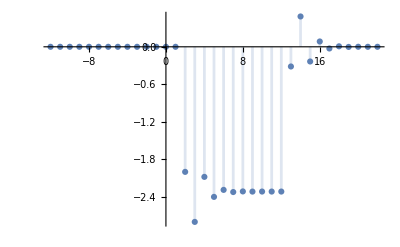

```mathematica
DiscretePlot[Piecewise[{{-14/5, k==3}, {-12/5, k==5}, {-7258/3125, k==7}, {-180888/78125, k==9}, {-180834/78125, k==10}, {-36136/15625, k==8}, {-286/125, k==6}, {-52/25, k==4}, {-2, k==2}, {2 (-1)^k 5^(2-k) (2299895110-387912327 k+16276042 k^2), k>10}, {0, True}}],{k,-12,22},PlotRange->All]
```

Altra definizione indiretta della funzione utilizzata come ingresso

## 7. Determinare, sul modello ARMA apposito, le condizioni iniziali tali che la risposta al gradino coincide con il suo valore di regime (assenza di componente transitoria).

Consideriamo come ingresso il gradino generico 𝑢(𝑘) = 𝑈 ∙ 1(𝑘)  con U numero reale.  Per prima cosa pero dobbiamo usare il modello arma per determinare le condizioni iniziali

```mathematica
Subscript[x, 0INC]={{Subscript[x, 1in]},{Subscript[x, 2in]},{Subscript[x, 3in]}}
```

{{x_in},{x_(2 in)},{x_(3 in)}}

Troviamo ora i corrispondenti stati nell’uscita

```mathematica
Subscript[y, 0INC] = (C1.Subscript[x, 0INC]) [[1,1]]
```

-4 x_in-2 x_(2 in)-2 x_(3 in)

```mathematica
Subscript[y, 1INC] = (C1.A.Subscript[x, 0INC]) [[1,1]]
```

-4 x_in-2 x_(2 in)-4 x_(3 in)

```mathematica
Subscript[y, 2INC] = (C1.A.A.Subscript[x, 0INC]) [[1,1]]
```

-(68 x_in)/125-(98 x_(2 in))/125-(14 x_(3 in))/25

```mathematica
(Collect[Solve[EqRz,Subscript[Y, iu][z]][[1,1]][[2]],Subscript[U, iu][z]])/.{y[0]->Subscript[y, 0INC] ,y[1]->Subscript[y, 1INC] ,y[2]->Subscript[y, 2INC] ,Subscript[U, iu][z]-> (z/(z-1))}
```

(5 (-50-50 z) z)/((-1+z) (1+5 z)^3)+(5 (15 z (-4 x_in-2 x_(2 in)-4 x_(3 in))+25 z^2 (-4 x_in-2 x_(2 in)-4 x_(3 in))+3 z (-4 x_in-2 x_(2 in)-2 x_(3 in))+15 z^2 (-4 x_in-2 x_(2 in)-2 x_(3 in))+25 z^3 (-4 x_in-2 x_(2 in)-2 x_(3 in))+25 z (-(68 x_in)/125-(98 x_(2 in))/125-(14 x_(3 in))/25)))/(1+5 z)^3

```mathematica
Subscript[Y, LIU][z_]:=Simplify[ (5 (15 z (-4 Subscript[x, in]-2 Subscript[x, 2 in]-4 Subscript[x, 3 in])+25 z^2 (-4 Subscript[x, in]-2 Subscript[x, 2 in]-4 Subscript[x, 3 in])+3 z (-4 Subscript[x, in]-2 Subscript[x, 2 in]-2 Subscript[x, 3 in])+15 z^2 (-4 Subscript[x, in]-2 Subscript[x, 2 in]-2 Subscript[x, 3 in])+25 z^3 (-4 Subscript[x, in]-2 Subscript[x, 2 in]-2 Subscript[x, 3 in])+25 z (-(68 Subscript[x, in])/125-(98 Subscript[x, 2 in])/125-(14 Subscript[x, 3 in])/25)))/(1+5 z)^3];Subscript[Y, LIU][z]
```

-(2 z ((214+400 z+250 z^2) x_in+(139+200 z+125 z^2) x_(2 in)+25 (8+13 z+5 z^2) x_(3 in)))/(1+5 z)^3

Rappresentazione della risposta libera + forzata modello ARMA, voglio ora trovarmi la componente transitoria

```mathematica
Subscript[Y, ssIU][z_]:= G[1](z/(z-1));
```

```mathematica
Subscript[Y, trIU][z_]:= Simplify[(5 (-50-50 z) z)/((-1+z) (1+5 z)^3) -Subscript[Y, ssIU][z]][[1,1]];Subscript[Y, trIU][z]
```

(125 z (107+200 z+125 z^2))/(54 (1+5 z)^3)

```mathematica
Subscript[Y, L-tr][z_]:= FullSimplify[Expand[Subscript[Y, trIU][z]+Subscript[Y, LIU][z]]];Subscript[Y, L-tr][z]
```

(z (-216 (107+25 z (8+5 z)) x_in-108 (139+25 z (8+5 z)) x_(2 in)+25 (535+125 z (8+5 z)-108 (1+z) (8+5 z) x_(3 in))))/(54 (1+5 z)^3)

```mathematica
coefList = CoefficientList[Numerator[Subscript[Y, L-tr][z]],z]
```

{0,13375-23112 x_in-15012 x_(2 in)-21600 x_(3 in),25000-43200 x_in-21600 x_(2 in)-35100 x_(3 in),15625-27000 x_in-13500 x_(2 in)-13500 x_(3 in)}

```mathematica
Solve[coefList =={0,0,0,0},{Subscript[x, in],Subscript[x, 2in],Subscript[x, 3in]}]
```

{{x_in→125/216,x_(2 in)→0,x_(3 in)→0}}

```mathematica
Subscript[x, new]={{125/216},{0},{0}}
```

{{125/216},{0},{0}}

Verifichiamo sia corretto

```mathematica
YL0[z_]:=Simplify[C1.(z Inverse[z IdentityMatrix[3]-A]).Subscript[x, new]];YL0[z]
```

{{-(125 z (107+200 z+125 z^2))/(54 (1+5 z)^3)}}

```mathematica
Together[Subscript[Y, trIU][z]]
```

(125 z (107+200 z+125 z^2))/(54 (1+5 z)^3)

Verifichiamo che la transitoria + la risposta libera si annullano in modo tale da lasciare che

```mathematica
Simplify[YL0[z]+Subscript[Y, trIU][z]]
```

{{0}}

```mathematica
YL0[z]+Subscript[Y, trIU][z] + Subscript[Y, ssIU][z]
```

{{-(125 z)/(54 (-1+z))}}

```mathematica
Subscript[Y, ssIU][z]
```

{{-(125 z)/(54 (-1+z))}}